```mathematica
(*ClearAll["Global`*"]*)
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COPEquilibrium/COPEquilibrium/copEquilibrium.txt";
data = Import[path,{"Table"}];
ListPlot[data,ImageSize->Large,AxesLabel->{"Passos de Monte Carlo","<ρ(y)>"}]
```

```mathematica
Export["/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COPEquilibrium/equilibrium2000.png",-Graphics-]
```

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COPEquilibrium/equilibrium2000.png

```mathematica
Export["/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COPEquilibrium/equilibrium20000.png",-Graphics-]
```

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COPEquilibrium/equilibrium20000.png

LeastSquares[{{0,0.25},{10,0.006},{20,0.0086},{30,0.0084},{40,0.011},{50,0.0112},{60,0.0112},{70,0.0148},{80,0.0132},{90,0.0156},{100,0.0152},{110,0.0158},{120,0.0152},{130,0.0182},{140,0.0158},{150,0.021},{160,0.0178},{170,0.0196},{180,0.0198},{190,0.0176},{200,0.0168},{210,0.018},{220,0.019},{230,0.0208},{240,0.0206},{250,0.017},{260,0.0184},{270,0.022},{280,0.0216},{290,0.021},{300,0.023},{310,0.0226},{320,0.0218},{330,0.0218},{340,0.0198},{350,0.0208},{360,0.0192},{370,0.0194},{380,0.023},{390,0.022},{400,0.0198},{410,0.0276},{420,0.0224},{430,0.0214},{440,0.0222},{450,0.022},{460,0.025},{470,0.0226},{480,0.0254},{490,0.0224},{500,0.0214},{510,0.0264},{520,0.0238},{530,0.0298},{540,0.0222},{550,0.025},{560,0.0214},{570,0.026},{580,0.0216},{590,0.0286},{600,0.0236},{610,0.0204},{620,0.0272},{630,0.0254},{640,0.0208},{650,0.0248},{660,0.029},{670,0.0294},{680,0.0272},{690,0.022},{700,0.0246},{710,0.025},{720,0.0262},{730,0.0238},{740,0.0286},{750,0.0256},{760,0.0262},{770,0.0246},{780,0.0232},{790,0.0232},{800,0.0288},{810,0.028},{820,0.0256},{830,0.0308},{840,0.03},{850,0.0244},{860,0.0276},{870,0.0314},{880,0.0256},{890,0.025},{900,0.0262},{910,0.0304},{920,0.0288},{930,0.0286},{940,0.0328},{950,0.027},{960,0.0272},{970,0.0272},{980,0.0286},{990,0.0306},{1000,0.0302},{1010,0.0286},{1020,0.0242},{1030,0.0266},{1040,0.0214},{1050,0.027},{1060,0.0254},{1070,0.0278},{1080,0.0268},{1090,0.024},{1100,0.0248},{1110,0.0272},{1120,0.03},{1130,0.0286},{1140,0.0292},{1150,0.0278},{1160,0.0272},{1170,0.0276},{1180,0.026},{1190,0.0292},{1200,0.0258},{1210,0.0274},{1220,0.0282},{1230,0.0278},{1240,0.0254},{1250,0.0274},{1260,0.0254},{1270,0.026},{1280,0.032},{1290,0.0296},{1300,0.0248},{1310,0.028},{1320,0.025},{1330,0.028},{1340,0.027},{1350,0.0338},{1360,0.0254},{1370,0.0272},{1380,0.027},{1390,0.0296},{1400,0.027},{1410,0.0244},{1420,0.0288},{1430,0.0304},{1440,0.024},{1450,0.0268},{1460,0.0286},{1470,0.0274},{1480,0.029},{1490,0.027},{1500,0.0274},{1510,0.0246},{1520,0.0296},{1530,0.0248},{1540,0.0278},{1550,0.0288},{1560,0.0276},{1570,0.03},{1580,0.0246},{1590,0.0292},{1600,0.0256},{1610,0.03},{1620,0.0238},{1630,0.0322},{1640,0.031},{1650,0.0332},{1660,0.0314},{1670,0.0272},{1680,0.0302},{1690,0.0298},{1700,0.0354},{1710,0.0294},{1720,0.0246},{1730,0.0272},{1740,0.0316},{1750,0.0274},{1760,0.0246},{1770,0.0278},{1780,0.0286},{1790,0.0296},{1800,0.0316},{1810,0.0258},{1820,0.0298},{1830,0.0272},{1840,0.033},{1850,0.032},{1860,0.0266},{1870,0.0272},{1880,0.027},{1890,0.028},{1900,0.0284},{1910,0.0298},{1920,0.0336},{1930,0.0296},{1940,0.0286},{1950,0.032},{1960,0.0286},{1970,0.028},{1980,0.0282},{1990,0.0256},{2000,0.0308},{2010,0.0316},{2020,0.0328},{2030,0.028},{2040,0.026},{2050,0.0284},{2060,0.0296},{2070,0.0292},{2080,0.0272},{2090,0.0266},{2100,0.0274},{2110,0.027},{2120,0.033},{2130,0.032},{2140,0.0288},{2150,0.028},{2160,0.032},{2170,0.0286},{2180,0.03},{2190,0.0284},{2200,0.0266},{2210,0.0278},{2220,0.03},{2230,0.0294},{2240,0.0284},{2250,0.0254},{2260,0.0282},{2270,0.0284},{2280,0.029},{2290,0.026},{2300,0.0308},{2310,0.0256},{2320,0.0308},{2330,0.0278},{2340,0.0306},{2350,0.0304},{2360,0.0264},{2370,0.0266},{2380,0.0274},{2390,0.0344},{2400,0.0298},{2410,0.0276},{2420,0.0276},{2430,0.0262},{2440,0.031},{2450,0.0294},{2460,0.0238},{2470,0.0336},{2480,0.0288},{2490,0.0282},{2500,0.0364},{2510,0.0276},{2520,0.0298},{2530,0.0272},{2540,0.0302},{2550,0.0276},{2560,0.0262},{2570,0.0268},{2580,0.0336},{2590,0.0232},{2600,0.0276},{2610,0.0282},{2620,0.0312},{2630,0.0282},{2640,0.0312},{2650,0.0314},{2660,0.0318},{2670,0.025},{2680,0.0276},{2690,0.029},{2700,0.022},{2710,0.0294},{2720,0.0232},{2730,0.0316},{2740,0.0302},{2750,0.028},{2760,0.0296},{2770,0.03},{2780,0.027},{2790,0.0302},{2800,0.03},{2810,0.028},{2820,0.0284},{2830,0.03},{2840,0.0278},{2850,0.0318},{2860,0.0268},{2870,0.0258},{2880,0.0268},{2890,0.0274},{2900,0.0266},{2910,0.028},{2920,0.0268},{2930,0.0318},{2940,0.024},{2950,0.0314},{2960,0.0314},{2970,0.0302},{2980,0.032},{2990,0.029},{3000,0.0278},{3010,0.0254},{3020,0.033},{3030,0.032},{3040,0.0298},{3050,0.0282},{3060,0.0296},{3070,0.0278},{3080,0.0326},{3090,0.028},{3100,0.0326},{3110,0.0328},{3120,0.0292},{3130,0.0254},{3140,0.0322},{3150,0.0328},{3160,0.0326},{3170,0.0298},{3180,0.03},{3190,0.034},{3200,0.0248},{3210,0.0336},{3220,0.0294},{3230,0.0342},{3240,0.0346},{3250,0.0336},{3260,0.031},{3270,0.0278},{3280,0.0288},{3290,0.0376},{3300,0.0336},{3310,0.03},{3320,0.0304},{3330,0.0312},{3340,0.0302},{3350,0.0302},{3360,0.0318},{3370,0.0302},{3380,0.0336},{3390,0.0322},{3400,0.0284},{3410,0.0292},{3420,0.0368},{3430,0.0318},{3440,0.0258},{3450,0.0286},{3460,0.0288},{3470,0.0314},{3480,0.0284},{3490,0.0328},{3500,0.032},{3510,0.0294},{3520,0.0288},{3530,0.026},{3540,0.0316},{3550,0.0254},{3560,0.0302},{3570,0.0266},{3580,0.0232},{3590,0.0312},{3600,0.031},{3610,0.0284},{3620,0.0356},{3630,0.031},{3640,0.0248},{3650,0.03},{3660,0.0292},{3670,0.0266},{3680,0.031},{3690,0.032},{3700,0.029},{3710,0.0306},{3720,0.0324},{3730,0.0274},{3740,0.028},{3750,0.0322},{3760,0.0328},{3770,0.029},{3780,0.0288},{3790,0.0298},{3800,0.0286},{3810,0.029},{3820,0.0262},{3830,0.0304},{3840,0.0322},{3850,0.032},{3860,0.0296},{3870,0.0272},{3880,0.0326},{3890,0.0334},{3900,0.026},{3910,0.0282},{3920,0.0352},{3930,0.034},{3940,0.0338},{3950,0.0256},{3960,0.0246},{3970,0.0246},{3980,0.0318},{3990,0.0328},{4000,0.0296},{4010,0.028},{4020,0.0288},{4030,0.0262},{4040,0.0334},{4050,0.0332},{4060,0.0286},{4070,0.0272},{4080,0.03},{4090,0.0254},{4100,0.0336},{4110,0.0278},{4120,0.0278},{4130,0.0294},{4140,0.0302},{4150,0.0294},{4160,0.0288},{4170,0.0312},{4180,0.0286},{4190,0.0302},{4200,0.0342},{4210,0.0296},{4220,0.0282},{4230,0.0342},{4240,0.0322},{4250,0.0286},{4260,0.0238},{4270,0.0288},{4280,0.0288},{4290,0.026},{4300,0.0298},{4310,0.0304},{4320,0.03},{4330,0.0344},{4340,0.0244},{4350,0.0316},{4360,0.0308},{4370,0.0266},{4380,0.0246},{4390,0.0326},{4400,0.0274},{4410,0.0332},{4420,0.0284},{4430,0.03},{4440,0.0324},{4450,0.0292},{4460,0.0258},{4470,0.0298},{4480,0.0312},{4490,0.0294},{4500,0.0306},{4510,0.0318},{4520,0.029},{4530,0.0294},{4540,0.0296},{4550,0.0314},{4560,0.0294},{4570,0.0266},{4580,0.0278},{4590,0.024},{4600,0.0292},{4610,0.0254},{4620,0.0294},{4630,0.0314},{4640,0.0258},{4650,0.0244},{4660,0.0308},{4670,0.0292},{4680,0.028},{4690,0.0236},{4700,0.0294},{4710,0.0322},{4720,0.0264},{4730,0.0306},{4740,0.0266},{4750,0.0284},{4760,0.0324},{4770,0.0312},{4780,0.0284},{4790,0.0298},{4800,0.0274},{4810,0.0274},{4820,0.0336},{4830,0.0306},{4840,0.0272},{4850,0.0282},{4860,0.0308},{4870,0.031},{4880,0.0254},{4890,0.0284},{4900,0.0316},{4910,0.0262},{4920,0.0346},{4930,0.0278},{4940,0.0318},{4950,0.0284},{4960,0.0282},{4970,0.033},{4980,0.028},{4990,0.0272},{5000,0.0324},{5010,0.0274},{5020,0.0334},{5030,0.0314},{5040,0.0296},{5050,0.0278},{5060,0.0348},{5070,0.0314},{5080,0.0308},{5090,0.028},{5100,0.0286},{5110,0.0326},{5120,0.0292},{5130,0.0318},{5140,0.0326},{5150,0.0322},{5160,0.0286},{5170,0.03},{5180,0.0306},{5190,0.0322},{5200,0.0274},{5210,0.0296},{5220,0.0268},{5230,0.0296},{5240,0.029},{5250,0.0282},{5260,0.0286},{5270,0.0286},{5280,0.033},{5290,0.0326},{5300,0.0304},{5310,0.0314},{5320,0.0298},{5330,0.03},{5340,0.0298},{5350,0.0328},{5360,0.0338},{5370,0.0294},{5380,0.0268},{5390,0.0244},{5400,0.0298},{5410,0.0286},{5420,0.0282},{5430,0.0328},{5440,0.0308},{5450,0.0284},{5460,0.0322},{5470,0.0316},{5480,0.0258},{5490,0.0312},{5500,0.0292},{5510,0.0258},{5520,0.0278},{5530,0.0282},{5540,0.029},{5550,0.028},{5560,0.031},{5570,0.0266},{5580,0.0276},{5590,0.031},{5600,0.0282},{5610,0.0274},{5620,0.0252},{5630,0.0338},{5640,0.0262},{5650,0.0296},{5660,0.0348},{5670,0.0282},{5680,0.0288},{5690,0.0302},{5700,0.032},{5710,0.032},{5720,0.0272},{5730,0.0284},{5740,0.0318},{5750,0.0272},{5760,0.0334},{5770,0.0254},{5780,0.0334},{5790,0.0292},{5800,0.0266},{5810,0.0342},{5820,0.0312},{5830,0.0248},{5840,0.0312},{5850,0.0288},{5860,0.0224},{5870,0.031},{5880,0.0318},{5890,0.035},{5900,0.0302},{5910,0.0348},{5920,0.03},{5930,0.026},{5940,0.0278},{5950,0.0286},{5960,0.031},{5970,0.0312},{5980,0.033},{5990,0.0332},{6000,0.0286},{6010,0.0292},{6020,0.0296},{6030,0.0296},{6040,0.0278},{6050,0.032},{6060,0.0278},{6070,0.0288},{6080,0.0298},{6090,0.0268},{6100,0.0322},{6110,0.032},{6120,0.03},{6130,0.0314},{6140,0.03},{6150,0.0218},{6160,0.0228},{6170,0.0312},{6180,0.0256},{6190,0.0276},{6200,0.0332},{6210,0.0294},{6220,0.0296},{6230,0.028},{6240,0.0284},{6250,0.029},{6260,0.03},{6270,0.0294},{6280,0.0278},{6290,0.03},{6300,0.028},{6310,0.0306},{6320,0.028},{6330,0.033},{6340,0.0256},{6350,0.0312},{6360,0.0316},{6370,0.0296},{6380,0.0274},{6390,0.0314},{6400,0.0268},{6410,0.0244},{6420,0.03},{6430,0.0302},{6440,0.0242},{6450,0.0288},{6460,0.025},{6470,0.0296},{6480,0.0294},{6490,0.0282},{6500,0.0268},{6510,0.033},{6520,0.0286},{6530,0.0272},{6540,0.0288},{6550,0.0278},{6560,0.0302},{6570,0.0322},{6580,0.0334},{6590,0.0308},{6600,0.0298},{6610,0.0316},{6620,0.034},{6630,0.03},{6640,0.031},{6650,0.0276},{6660,0.0246},{6670,0.0298},{6680,0.0234},{6690,0.0324},{6700,0.032},{6710,0.0296},{6720,0.0258},{6730,0.027},{6740,0.0304},{6750,0.0306},{6760,0.031},{6770,0.0336},{6780,0.0298},{6790,0.0298},{6800,0.0322},{6810,0.0262},{6820,0.03},{6830,0.0332},{6840,0.0296},{6850,0.031},{6860,0.0266},{6870,0.0348},{6880,0.0274},{6890,0.0288},{6900,0.0314},{6910,0.0298},{6920,0.0304},{6930,0.028},{6940,0.0294},{6950,0.0256},{6960,0.0318},{6970,0.028},{6980,0.0248},{6990,0.0298},{7000,0.028},{7010,0.0292},{7020,0.0294},{7030,0.0274},{7040,0.0292},{7050,0.0306},{7060,0.0356},{7070,0.032},{7080,0.029},{7090,0.0296},{7100,0.0278},{7110,0.0308},{7120,0.0284},{7130,0.0284},{7140,0.026},{7150,0.0316},{7160,0.029},{7170,0.0306},{7180,0.031},{7190,0.0312},{7200,0.0288},{7210,0.0284},{7220,0.032},{7230,0.0328},{7240,0.0254},{7250,0.0292},{7260,0.0292},{7270,0.0242},{7280,0.032},{7290,0.0278},{7300,0.0304},{7310,0.0278},{7320,0.032},{7330,0.0312},{7340,0.0308},{7350,0.029},{7360,0.0266},{7370,0.0308},{7380,0.0294},{7390,0.03},{7400,0.0282},{7410,0.029},{7420,0.029},{7430,0.0246},{7440,0.033},{7450,0.0274},{7460,0.0304},{7470,0.0296},{7480,0.0292},{7490,0.0304},{7500,0.0334},{7510,0.0344},{7520,0.0248},{7530,0.0306},{7540,0.0288},{7550,0.0248},{7560,0.0266},{7570,0.0354},{7580,0.0294},{7590,0.0286},{7600,0.03},{7610,0.0246},{7620,0.028},{7630,0.0286},{7640,0.0306},{7650,0.027},{7660,0.0304},{7670,0.033},{7680,0.0308},{7690,0.0294},{7700,0.0306},{7710,0.03},{7720,0.028},{7730,0.0274},{7740,0.0292},{7750,0.03},{7760,0.03},{7770,0.0308},{7780,0.0308},{7790,0.026},{7800,0.0272},{7810,0.0306},{7820,0.0258},{7830,0.0298},{7840,0.031},{7850,0.0268},{7860,0.0292},{7870,0.028},{7880,0.038},{7890,0.028},{7900,0.0278},{7910,0.0306},{7920,0.0268},{7930,0.0306},{7940,0.0358},{7950,0.0292},{7960,0.0328},{7970,0.0276},{7980,0.0294},{7990,0.0314},{8000,0.027},{8010,0.0282},{8020,0.0274},{8030,0.033},{8040,0.0298},{8050,0.0306},{8060,0.0284},{8070,0.0306},{8080,0.029},{8090,0.0308},{8100,0.03},{8110,0.0278},{8120,0.0266},{8130,0.0332},{8140,0.03},{8150,0.0316},{8160,0.031},{8170,0.0288},{8180,0.0268},{8190,0.0244},{8200,0.0296},{8210,0.0294},{8220,0.029},{8230,0.0264},{8240,0.0292},{8250,0.0312},{8260,0.0284},{8270,0.029},{8280,0.036},{8290,0.0274},{8300,0.0318},{8310,0.027},{8320,0.027},{8330,0.0296},{8340,0.0296},{8350,0.0264},{8360,0.0302},{8370,0.03},{8380,0.0248},{8390,0.032},{8400,0.0276},{8410,0.0334},{8420,0.029},{8430,0.035},{8440,0.0272},{8450,0.0268},{8460,0.0296},{8470,0.0294},{8480,0.0278},{8490,0.0296},{8500,0.03},{8510,0.0282},{8520,0.0296},{8530,0.0304},{8540,0.027},{8550,0.0308},{8560,0.0298},{8570,0.0292},{8580,0.0328},{8590,0.0316},{8600,0.0252},{8610,0.0312},{8620,0.0316},{8630,0.0314},{8640,0.0314},{8650,0.026},{8660,0.0282},{8670,0.0304},{8680,0.0298},{8690,0.0286},{8700,0.028},{8710,0.0358},{8720,0.0322},{8730,0.0334},{8740,0.0308},{8750,0.0284},{8760,0.032},{8770,0.0264},{8780,0.0246},{8790,0.03},{8800,0.03},{8810,0.0294},{8820,0.0282},{8830,0.0316},{8840,0.0302},{8850,0.0286},{8860,0.0286},{8870,0.032},{8880,0.0298},{8890,0.0238},{8900,0.029},{8910,0.0308},{8920,0.03},{8930,0.0296},{8940,0.0278},{8950,0.0332},{8960,0.026},{8970,0.032},{8980,0.028},{8990,0.0282},{9000,0.0318},{9010,0.0344},{9020,0.0284},{9030,0.0314},{9040,0.0314},{9050,0.0296},{9060,0.0292},{9070,0.028},{9080,0.0302},{9090,0.0294},{9100,0.0294},{9110,0.0258},{9120,0.032},{9130,0.0342},{9140,0.0284},{9150,0.0278},{9160,0.0284},{9170,0.0236},{9180,0.032},{9190,0.0288},{9200,0.031},{9210,0.028},{9220,0.0258},{9230,0.0348},{9240,0.0318},{9250,0.029},{9260,0.0306},{9270,0.029},{9280,0.029},{9290,0.0376},{9300,0.0292},{9310,0.0354},{9320,0.0308},{9330,0.0296},{9340,0.0326},{9350,0.0252},{9360,0.0258},{9370,0.0262},{9380,0.0292},{9390,0.0322},{9400,0.0324},{9410,0.0282},{9420,0.0336},{9430,0.0298},{9440,0.0292},{9450,0.0268},{9460,0.0282},{9470,0.032},{9480,0.0332},{9490,0.0364},{9500,0.0294},{9510,0.032},{9520,0.028},{9530,0.0242},{9540,0.0292},{9550,0.0298},{9560,0.0284},{9570,0.0272},{9580,0.0344},{9590,0.0304},{9600,0.0328},{9610,0.031},{9620,0.0302},{9630,0.0316},{9640,0.0328},{9650,0.0328},{9660,0.0262},{9670,0.0324},{9680,0.028},{9690,0.0276},{9700,0.0258},{9710,0.0262},{9720,0.028},{9730,0.0274},{9740,0.0294},{9750,0.0314},{9760,0.0302},{9770,0.0322},{9780,0.0274},{9790,0.0288},{9800,0.0288},{9810,0.0318},{9820,0.0302},{9830,0.0312},{9840,0.0352},{9850,0.0256},{9860,0.027},{9870,0.0314},{9880,0.028},{9890,0.026},{9900,0.033},{9910,0.0284},{9920,0.0354},{9930,0.0282},{9940,0.0332},{9950,0.0296},{9960,0.0304},{9970,0.0264},{9980,0.0292},{9990,0.0334},{10000,0.0328},{10010,0.031},{10020,0.0292},{10030,0.0294},{10040,0.0288},{10050,0.027},{10060,0.0294},{10070,0.0278},{10080,0.0298},{10090,0.0268},{10100,0.0322},{10110,0.027},{10120,0.0312},{10130,0.0326},{10140,0.0262},{10150,0.0346},{10160,0.0344},{10170,0.0302},{10180,0.0274},{10190,0.0278},{10200,0.0296},{10210,0.0344},{10220,0.0276},{10230,0.0302},{10240,0.024},{10250,0.0322},{10260,0.0292},{10270,0.0338},{10280,0.031},{10290,0.0246},{10300,0.0316},{10310,0.0254},{10320,0.0332},{10330,0.0322},{10340,0.0252},{10350,0.0308},{10360,0.0304},{10370,0.0294},{10380,0.0316},{10390,0.0314},{10400,0.0322},{10410,0.0312},{10420,0.0296},{10430,0.03},{10440,0.0296},{10450,0.029},{10460,0.0326},{10470,0.0294},{10480,0.0262},{10490,0.0302},{10500,0.029},{10510,0.0316},{10520,0.0316},{10530,0.0352},{10540,0.0282},{10550,0.0358},{10560,0.029},{10570,0.0224},{10580,0.0274},{10590,0.029},{10600,0.0286},{10610,0.0304},{10620,0.0262},{10630,0.0262},{10640,0.0332},{10650,0.0322},{10660,0.0284},{10670,0.0328},{10680,0.032},{10690,0.0296},{10700,0.028},{10710,0.0296},{10720,0.0272},{10730,0.0338},{10740,0.0318},{10750,0.0312},{10760,0.0302},{10770,0.0282},{10780,0.0312},{10790,0.0348},{10800,0.0296},{10810,0.033},{10820,0.0266},{10830,0.0278},{10840,0.0286},{10850,0.0308},{10860,0.0266},{10870,0.0314},{10880,0.0292},{10890,0.0248},{10900,0.0304},{10910,0.0284},{10920,0.0284},{10930,0.0302},{10940,0.0322},{10950,0.0368},{10960,0.032},{10970,0.028},{10980,0.028},{10990,0.0326},{11000,0.027},{11010,0.028},{11020,0.0304},{11030,0.031},{11040,0.034},{11050,0.0278},{11060,0.0302},{11070,0.0294},{11080,0.0302},{11090,0.0324},{11100,0.031},{11110,0.0296},{11120,0.0294},{11130,0.0314},{11140,0.027},{11150,0.0294},{11160,0.0276},{11170,0.0322},{11180,0.0272},{11190,0.0292},{11200,0.028},{11210,0.0306},{11220,0.03},{11230,0.0314},{11240,0.0308},{11250,0.0338},{11260,0.033},{11270,0.0278},{11280,0.0334},{11290,0.0318},{11300,0.0294},{11310,0.0352},{11320,0.0314},{11330,0.0322},{11340,0.0322},{11350,0.0298},{11360,0.0292},{11370,0.0282},{11380,0.0294},{11390,0.031},{11400,0.032},{11410,0.0282},{11420,0.0294},{11430,0.0326},{11440,0.0258},{11450,0.0268},{11460,0.0332},{11470,0.029},{11480,0.0302},{11490,0.0314},{11500,0.0342},{11510,0.0258},{11520,0.0244},{11530,0.0314},{11540,0.0292},{11550,0.0318},{11560,0.0306},{11570,0.034},{11580,0.035},{11590,0.0302},{11600,0.0292},{11610,0.0292},{11620,0.0308},{11630,0.0292},{11640,0.0332},{11650,0.0318},{11660,0.0296},{11670,0.0262},{11680,0.0326},{11690,0.0308},{11700,0.0288},{11710,0.0334},{11720,0.0254},{11730,0.0324},{11740,0.0342},{11750,0.0276},{11760,0.0296},{11770,0.0274},{11780,0.0326},{11790,0.0308},{11800,0.0276},{11810,0.028},{11820,0.03},{11830,0.0318},{11840,0.0336},{11850,0.035},{11860,0.029},{11870,0.0302},{11880,0.0308},{11890,0.027},{11900,0.031},{11910,0.0312},{11920,0.032},{11930,0.0312},{11940,0.025},{11950,0.0274},{11960,0.0302},{11970,0.0282},{11980,0.0334},{11990,0.03},{12000,0.0254},{12010,0.032},{12020,0.0286},{12030,0.0286},{12040,0.0292},{12050,0.026},{12060,0.0308},{12070,0.0276},{12080,0.0294},{12090,0.031},{12100,0.0318},{12110,0.029},{12120,0.0288},{12130,0.0364},{12140,0.0272},{12150,0.0252},{12160,0.0338},{12170,0.036},{12180,0.029},{12190,0.0328},{12200,0.032},{12210,0.0284},{12220,0.029},{12230,0.027},{12240,0.028},{12250,0.0328},{12260,0.0286},{12270,0.0334},{12280,0.0346},{12290,0.0314},{12300,0.03},{12310,0.0358},{12320,0.0312},{12330,0.0298},{12340,0.0312},{12350,0.028},{12360,0.0224},{12370,0.0288},{12380,0.0296},{12390,0.029},{12400,0.0318},{12410,0.0238},{12420,0.0314},{12430,0.03},{12440,0.0292},{12450,0.0274},{12460,0.0316},{12470,0.029},{12480,0.0346},{12490,0.0264},{12500,0.0308},{12510,0.0268},{12520,0.0316},{12530,0.0268},{12540,0.0268},{12550,0.0284},{12560,0.032},{12570,0.0288},{12580,0.0304},{12590,0.0286},{12600,0.0336},{12610,0.0316},{12620,0.0342},{12630,0.0326},{12640,0.0256},{12650,0.0288},{12660,0.025},{12670,0.029},{12680,0.0282},{12690,0.0296},{12700,0.0298},{12710,0.0256},{12720,0.0282},{12730,0.0324},{12740,0.0312},{12750,0.0298},{12760,0.0326},{12770,0.0302},{12780,0.0272},{12790,0.0296},{12800,0.0348},{12810,0.0262},{12820,0.032},{12830,0.0284},{12840,0.0318},{12850,0.0252},{12860,0.0336},{12870,0.0308},{12880,0.0294},{12890,0.0292},{12900,0.0288},{12910,0.0292},{12920,0.0278},{12930,0.0366},{12940,0.031},{12950,0.0256},{12960,0.0244},{12970,0.0302},{12980,0.032},{12990,0.031},{13000,0.0308},{13010,0.0296},{13020,0.0308},{13030,0.0284},{13040,0.028},{13050,0.0302},{13060,0.0328},{13070,0.0338},{13080,0.0312},{13090,0.0314},{13100,0.0292},{13110,0.032},{13120,0.0296},{13130,0.0262},{13140,0.0284},{13150,0.0296},{13160,0.0298},{13170,0.0286},{13180,0.0288},{13190,0.0268},{13200,0.0298},{13210,0.0294},{13220,0.03},{13230,0.028},{13240,0.0262},{13250,0.0342},{13260,0.0244},{13270,0.0288},{13280,0.0304},{13290,0.027},{13300,0.0314},{13310,0.0278},{13320,0.0344},{13330,0.0304},{13340,0.0264},{13350,0.0324},{13360,0.0326},{13370,0.0264},{13380,0.0298},{13390,0.0334},{13400,0.028},{13410,0.036},{13420,0.0318},{13430,0.0302},{13440,0.028},{13450,0.0288},{13460,0.0286},{13470,0.0344},{13480,0.0262},{13490,0.0316},{13500,0.0358},{13510,0.0318},{13520,0.029},{13530,0.03},{13540,0.032},{13550,0.0256},{13560,0.027},{13570,0.03},{13580,0.0274},{13590,0.0318},{13600,0.032},{13610,0.0244},{13620,0.0322},{13630,0.0324},{13640,0.0264},{13650,0.0254},{13660,0.0304},{13670,0.0334},{13680,0.0312},{13690,0.024},{13700,0.0272},{13710,0.0304},{13720,0.0282},{13730,0.024},{13740,0.029},{13750,0.0358},{13760,0.0348},{13770,0.0318},{13780,0.0286},{13790,0.0282},{13800,0.0286},{13810,0.0324},{13820,0.0296},{13830,0.0334},{13840,0.0306},{13850,0.0284},{13860,0.0272},{13870,0.0298},{13880,0.0272},{13890,0.0268},{13900,0.0318},{13910,0.0338},{13920,0.0318},{13930,0.0294},{13940,0.0252},{13950,0.033},{13960,0.033},{13970,0.0274},{13980,0.0336},{13990,0.0298},{14000,0.0266},{14010,0.0294},{14020,0.0288},{14030,0.0318},{14040,0.0298},{14050,0.0304},{14060,0.0312},{14070,0.0284},{14080,0.0324},{14090,0.0308},{14100,0.0306},{14110,0.0274},{14120,0.0298},{14130,0.0322},{14140,0.0342},{14150,0.0292},{14160,0.0264},{14170,0.03},{14180,0.0322},{14190,0.0314},{14200,0.0278},{14210,0.0272},{14220,0.0352},{14230,0.0314},{14240,0.033},{14250,0.0276},{14260,0.0328},{14270,0.029},{14280,0.0298},{14290,0.0328},{14300,0.031},{14310,0.0318},{14320,0.0296},{14330,0.0308},{14340,0.0326},{14350,0.0326},{14360,0.0328},{14370,0.032},{14380,0.0324},{14390,0.0286},{14400,0.0276},{14410,0.0272},{14420,0.0254},{14430,0.0344},{14440,0.0312},{14450,0.0294},{14460,0.0288},{14470,0.0318},{14480,0.029},{14490,0.0308},{14500,0.03},{14510,0.0302},{14520,0.0322},{14530,0.0252},{14540,0.0304},{14550,0.0246},{14560,0.031},{14570,0.0302},{14580,0.031},{14590,0.0296},{14600,0.0332},{14610,0.036},{14620,0.0304},{14630,0.0328},{14640,0.0282},{14650,0.0356},{14660,0.0284},{14670,0.0284},{14680,0.0274},{14690,0.0304},{14700,0.0246},{14710,0.0334},{14720,0.0332},{14730,0.0266},{14740,0.03},{14750,0.0324},{14760,0.0246},{14770,0.0306},{14780,0.0316},{14790,0.031},{14800,0.0282},{14810,0.0294},{14820,0.029},{14830,0.0272},{14840,0.0294},{14850,0.0256},{14860,0.0306},{14870,0.0338},{14880,0.0328},{14890,0.0298},{14900,0.0314},{14910,0.0278},{14920,0.0326},{14930,0.0342},{14940,0.0266},{14950,0.0294},{14960,0.03},{14970,0.0284},{14980,0.0296},{14990,0.0296},{15000,0.0308},{15010,0.0268},{15020,0.0232},{15030,0.0272},{15040,0.0276},{15050,0.027},{15060,0.0286},{15070,0.0336},{15080,0.0324},{15090,0.0298},{15100,0.0298},{15110,0.0296},{15120,0.0318},{15130,0.0302},{15140,0.0302},{15150,0.0292},{15160,0.0288},{15170,0.0312},{15180,0.0324},{15190,0.032},{15200,0.0298},{15210,0.033},{15220,0.0322},{15230,0.0308},{15240,0.0286},{15250,0.0284},{15260,0.0308},{15270,0.0278},{15280,0.0284},{15290,0.027},{15300,0.0294},{15310,0.0288},{15320,0.0346},{15330,0.0298},{15340,0.0254},{15350,0.0288},{15360,0.029},{15370,0.0342},{15380,0.0302},{15390,0.0296},{15400,0.0318},{15410,0.0244},{15420,0.0302},{15430,0.0286},{15440,0.0314},{15450,0.0306},{15460,0.0288},{15470,0.0304},{15480,0.0284},{15490,0.0296},{15500,0.0292},{15510,0.0278},{15520,0.026},{15530,0.0342},{15540,0.0306},{15550,0.0296},{15560,0.029},{15570,0.032},{15580,0.0316},{15590,0.0308},{15600,0.0362},{15610,0.036},{15620,0.0314},{15630,0.0272},{15640,0.0304},{15650,0.0284},{15660,0.0314},{15670,0.0316},{15680,0.0282},{15690,0.0264},{15700,0.0294},{15710,0.028},{15720,0.028},{15730,0.03},{15740,0.0266},{15750,0.023},{15760,0.0238},{15770,0.0302},{15780,0.0322},{15790,0.0342},{15800,0.0288},{15810,0.0296},{15820,0.031},{15830,0.0296},{15840,0.0262},{15850,0.0314},{15860,0.03},{15870,0.032},{15880,0.0304},{15890,0.0264},{15900,0.0332},{15910,0.03},{15920,0.033},{15930,0.0288},{15940,0.0326},{15950,0.036},{15960,0.0268},{15970,0.035},{15980,0.029},{15990,0.0316},{16000,0.035},{16010,0.0334},{16020,0.031},{16030,0.0308},{16040,0.028},{16050,0.0292},{16060,0.0354},{16070,0.0286},{16080,0.0306},{16090,0.0266},{16100,0.0356},{16110,0.0274},{16120,0.027},{16130,0.0258},{16140,0.03},{16150,0.031},{16160,0.0256},{16170,0.0288},{16180,0.0338},{16190,0.0278},{16200,0.0322},{16210,0.0314},{16220,0.0292},{16230,0.0312},{16240,0.0296},{16250,0.0268},{16260,0.0312},{16270,0.0276},{16280,0.0292},{16290,0.026},{16300,0.026},{16310,0.0318},{16320,0.0272},{16330,0.0284},{16340,0.0324},{16350,0.03},{16360,0.0242},{16370,0.0312},{16380,0.035},{16390,0.025},{16400,0.0314},{16410,0.03},{16420,0.0338},{16430,0.0294},{16440,0.0334},{16450,0.031},{16460,0.0288},{16470,0.03},{16480,0.0268},{16490,0.0272},{16500,0.0286},{16510,0.0316},{16520,0.0318},{16530,0.0326},{16540,0.0306},{16550,0.03},{16560,0.027},{16570,0.026},{16580,0.0274},{16590,0.0312},{16600,0.0346},{16610,0.0286},{16620,0.031},{16630,0.0278},{16640,0.0272},{16650,0.0304},{16660,0.0278},{16670,0.0324},{16680,0.0274},{16690,0.0266},{16700,0.0282},{16710,0.0336},{16720,0.0292},{16730,0.0296},{16740,0.0286},{16750,0.0278},{16760,0.0336},{16770,0.032},{16780,0.0286},{16790,0.0288},{16800,0.0264},{16810,0.0284},{16820,0.0338},{16830,0.024},{16840,0.0294},{16850,0.0252},{16860,0.0332},{16870,0.0344},{16880,0.033},{16890,0.0368},{16900,0.0256},{16910,0.0226},{16920,0.0346},{16930,0.0288},{16940,0.0296},{16950,0.0276},{16960,0.0276},{16970,0.0314},{16980,0.0266},{16990,0.0274},{17000,0.0286},{17010,0.0302},{17020,0.0292},{17030,0.0332},{17040,0.03},{17050,0.0334},{17060,0.0322},{17070,0.0262},{17080,0.0294},{17090,0.0292},{17100,0.0294},{17110,0.031},{17120,0.0314},{17130,0.0282},{17140,0.0302},{17150,0.03},{17160,0.0296},{17170,0.0326},{17180,0.0294},{17190,0.0338},{17200,0.0322},{17210,0.0248},{17220,0.0298},{17230,0.0296},{17240,0.026},{17250,0.0246},{17260,0.0328},{17270,0.0298},{17280,0.032},{17290,0.0328},{17300,0.0344},{17310,0.028},{17320,0.0272},{17330,0.0314},{17340,0.0318},{17350,0.0362},{17360,0.0274},{17370,0.031},{17380,0.027},{17390,0.031},{17400,0.0296},{17410,0.029},{17420,0.0286},{17430,0.0254},{17440,0.0328},{17450,0.0292},{17460,0.0312},{17470,0.0272},{17480,0.0312},{17490,0.0268},{17500,0.026},{17510,0.0288},{17520,0.029},{17530,0.0258},{17540,0.0274},{17550,0.0324},{17560,0.0298},{17570,0.0324},{17580,0.0266},{17590,0.0312},{17600,0.0282},{17610,0.0264},{17620,0.0268},{17630,0.0316},{17640,0.027},{17650,0.0292},{17660,0.0294},{17670,0.0318},{17680,0.0318},{17690,0.0296},{17700,0.0312},{17710,0.0232},{17720,0.029},{17730,0.0266},{17740,0.0314},{17750,0.0264},{17760,0.0282},{17770,0.035},{17780,0.0322},{17790,0.0252},{17800,0.0306},{17810,0.0322},{17820,0.0302},{17830,0.0288},{17840,0.033},{17850,0.0278},{17860,0.0238},{17870,0.0284},{17880,0.0302},{17890,0.0272},{17900,0.026},{17910,0.0282},{17920,0.0244},{17930,0.0326},{17940,0.0296},{17950,0.0312},{17960,0.03},{17970,0.0286},{17980,0.0262},{17990,0.0342},{18000,0.0308},{18010,0.0326},{18020,0.0332},{18030,0.035},{18040,0.0298},{18050,0.0274},{18060,0.0278},{18070,0.0362},{18080,0.0278},{18090,0.0324},{18100,0.0308},{18110,0.0344},{18120,0.0248},{18130,0.0322},{18140,0.0282},{18150,0.0244},{18160,0.0302},{18170,0.0294},{18180,0.0302},{18190,0.0266},{18200,0.0342},{18210,0.0324},{18220,0.0278},{18230,0.0342},{18240,0.029},{18250,0.03},{18260,0.031},{18270,0.0308},{18280,0.0248},{18290,0.0282},{18300,0.029},{18310,0.0272},{18320,0.0326},{18330,0.0328},{18340,0.0302},{18350,0.0256},{18360,0.0316},{18370,0.0326},{18380,0.0296},{18390,0.0268},{18400,0.0296},{18410,0.0338},{18420,0.031},{18430,0.027},{18440,0.0284},{18450,0.0344},{18460,0.032},{18470,0.0324},{18480,0.0262},{18490,0.0284},{18500,0.0268},{18510,0.0334},{18520,0.032},{18530,0.0288},{18540,0.0294},{18550,0.0298},{18560,0.0282},{18570,0.0316},{18580,0.0286},{18590,0.0228},{18600,0.0372},{18610,0.0248},{18620,0.0318},{18630,0.028},{18640,0.0246},{18650,0.0308},{18660,0.029},{18670,0.0274},{18680,0.03},{18690,0.0292},{18700,0.0262},{18710,0.0288},{18720,0.0286},{18730,0.0296},{18740,0.0316},{18750,0.0312},{18760,0.0284},{18770,0.0278},{18780,0.031},{18790,0.0332},{18800,0.0278},{18810,0.0272},{18820,0.033},{18830,0.034},{18840,0.0316},{18850,0.0352},{18860,0.026},{18870,0.0294},{18880,0.03},{18890,0.03},{18900,0.0316},{18910,0.031},{18920,0.0296},{18930,0.0272},{18940,0.0334},{18950,0.029},{18960,0.0278},{18970,0.031},{18980,0.0268},{18990,0.0342},{19000,0.0312},{19010,0.028},{19020,0.0292},{19030,0.0308},{19040,0.0314},{19050,0.027},{19060,0.0314},{19070,0.0286},{19080,0.0298},{19090,0.0288},{19100,0.033},{19110,0.0298},{19120,0.029},{19130,0.0284},{19140,0.0266},{19150,0.0284},{19160,0.031},{19170,0.0276},{19180,0.0332},{19190,0.03},{19200,0.0264},{19210,0.0258},{19220,0.0322},{19230,0.0254},{19240,0.0278},{19250,0.0284},{19260,0.0314},{19270,0.03},{19280,0.0272},{19290,0.031},{19300,0.0284},{19310,0.0278},{19320,0.0286},{19330,0.031},{19340,0.0322},{19350,0.029},{19360,0.032},{19370,0.0252},{19380,0.0262},{19390,0.0296},{19400,0.0334},{19410,0.0306},{19420,0.0266},{19430,0.0288},{19440,0.0288},{19450,0.0274},{19460,0.0262},{19470,0.0282},{19480,0.0256},{19490,0.0306},{19500,0.0248},{19510,0.0342},{19520,0.0274},{19530,0.028},{19540,0.0302},{19550,0.029},{19560,0.0298},{19570,0.0326},{19580,0.0312},{19590,0.026},{19600,0.0344},{19610,0.029},{19620,0.0292},{19630,0.0328},{19640,0.025},{19650,0.0282},{19660,0.0272},{19670,0.0304},{19680,0.0302},{19690,0.0314},{19700,0.0278},{19710,0.0316},{19720,0.0342},{19730,0.0312},{19740,0.0306},{19750,0.0316},{19760,0.0302},{19770,0.03},{19780,0.024},{19790,0.0274},{19800,0.0276},{19810,0.0272},{19820,0.03},{19830,0.0304},{19840,0.0326},{19850,0.0282},{19860,0.0286},{19870,0.0304},{19880,0.0324},{19890,0.0266},{19900,0.035},{19910,0.03},{19920,0.027},{19930,0.0264},{19940,0.034},{19950,0.0294},{19960,0.0292},{19970,0.033},{19980,0.033},{19990,0.0268}},{7,7}]

```mathematica
LeastSquares[Take[data,{1,20000,10}],{7,7}]
```

LeastSquares::lslc: Coefficient matrix and target vector(s) or matrix do not have the same dimensions.

LeastSquares[{{0,0.25},{10,0.006},{20,0.0086},{30,0.0084},{40,0.011},{50,0.0112},{60,0.0112},{70,0.0148},{80,0.0132},{90,0.0156},{100,0.0152},{110,0.0158},{120,0.0152},{130,0.0182},{140,0.0158},{150,0.021},{160,0.0178},{170,0.0196},{180,0.0198},{190,0.0176},{200,0.0168},{210,0.018},{220,0.019},{230,0.0208},{240,0.0206},{250,0.017},{260,0.0184},{270,0.022},{280,0.0216},{290,0.021},{300,0.023},{310,0.0226},{320,0.0218},{330,0.0218},{340,0.0198},{350,0.0208},{360,0.0192},{370,0.0194},{380,0.023},{390,0.022},{400,0.0198},{410,0.0276},{420,0.0224},{430,0.0214},{440,0.0222},{450,0.022},{460,0.025},{470,0.0226},{480,0.0254},{490,0.0224},{500,0.0214},{510,0.0264},{520,0.0238},{530,0.0298},{540,0.0222},{550,0.025},{560,0.0214},{570,0.026},{580,0.0216},{590,0.0286},{600,0.0236},{610,0.0204},{620,0.0272},{630,0.0254},{640,0.0208},{650,0.0248},{660,0.029},{670,0.0294},{680,0.0272},{690,0.022},{700,0.0246},{710,0.025},{720,0.0262},{730,0.0238},{740,0.0286},{750,0.0256},{760,0.0262},{770,0.0246},{780,0.0232},{790,0.0232},{800,0.0288},{810,0.028},{820,0.0256},{830,0.0308},{840,0.03},{850,0.0244},{860,0.0276},{870,0.0314},{880,0.0256},{890,0.025},{900,0.0262},{910,0.0304},{920,0.0288},{930,0.0286},{940,0.0328},{950,0.027},{960,0.0272},{970,0.0272},{980,0.0286},{990,0.0306},{1000,0.0302},{1010,0.0286},{1020,0.0242},{1030,0.0266},{1040,0.0214},{1050,0.027},{1060,0.0254},{1070,0.0278},{1080,0.0268},{1090,0.024},{1100,0.0248},{1110,0.0272},{1120,0.03},{1130,0.0286},{1140,0.0292},{1150,0.0278},{1160,0.0272},{1170,0.0276},{1180,0.026},{1190,0.0292},{1200,0.0258},{1210,0.0274},{1220,0.0282},{1230,0.0278},{1240,0.0254},{1250,0.0274},{1260,0.0254},{1270,0.026},{1280,0.032},{1290,0.0296},{1300,0.0248},{1310,0.028},{1320,0.025},{1330,0.028},{1340,0.027},{1350,0.0338},{1360,0.0254},{1370,0.0272},{1380,0.027},{1390,0.0296},{1400,0.027},{1410,0.0244},{1420,0.0288},{1430,0.0304},{1440,0.024},{1450,0.0268},{1460,0.0286},{1470,0.0274},{1480,0.029},{1490,0.027},{1500,0.0274},{1510,0.0246},{1520,0.0296},{1530,0.0248},{1540,0.0278},{1550,0.0288},{1560,0.0276},{1570,0.03},{1580,0.0246},{1590,0.0292},{1600,0.0256},{1610,0.03},{1620,0.0238},{1630,0.0322},{1640,0.031},{1650,0.0332},{1660,0.0314},{1670,0.0272},{1680,0.0302},{1690,0.0298},{1700,0.0354},{1710,0.0294},{1720,0.0246},{1730,0.0272},{1740,0.0316},{1750,0.0274},{1760,0.0246},{1770,0.0278},{1780,0.0286},{1790,0.0296},{1800,0.0316},{1810,0.0258},{1820,0.0298},{1830,0.0272},{1840,0.033},{1850,0.032},{1860,0.0266},{1870,0.0272},{1880,0.027},{1890,0.028},{1900,0.0284},{1910,0.0298},{1920,0.0336},{1930,0.0296},{1940,0.0286},{1950,0.032},{1960,0.0286},{1970,0.028},{1980,0.0282},{1990,0.0256},{2000,0.0308},{2010,0.0316},{2020,0.0328},{2030,0.028},{2040,0.026},{2050,0.0284},{2060,0.0296},{2070,0.0292},{2080,0.0272},{2090,0.0266},{2100,0.0274},{2110,0.027},{2120,0.033},{2130,0.032},{2140,0.0288},{2150,0.028},{2160,0.032},{2170,0.0286},{2180,0.03},{2190,0.0284},{2200,0.0266},{2210,0.0278},{2220,0.03},{2230,0.0294},{2240,0.0284},{2250,0.0254},{2260,0.0282},{2270,0.0284},{2280,0.029},{2290,0.026},{2300,0.0308},{2310,0.0256},{2320,0.0308},{2330,0.0278},{2340,0.0306},{2350,0.0304},{2360,0.0264},{2370,0.0266},{2380,0.0274},{2390,0.0344},{2400,0.0298},{2410,0.0276},{2420,0.0276},{2430,0.0262},{2440,0.031},{2450,0.0294},{2460,0.0238},{2470,0.0336},{2480,0.0288},{2490,0.0282},{2500,0.0364},{2510,0.0276},{2520,0.0298},{2530,0.0272},{2540,0.0302},{2550,0.0276},{2560,0.0262},{2570,0.0268},{2580,0.0336},{2590,0.0232},{2600,0.0276},{2610,0.0282},{2620,0.0312},{2630,0.0282},{2640,0.0312},{2650,0.0314},{2660,0.0318},{2670,0.025},{2680,0.0276},{2690,0.029},{2700,0.022},{2710,0.0294},{2720,0.0232},{2730,0.0316},{2740,0.0302},{2750,0.028},{2760,0.0296},{2770,0.03},{2780,0.027},{2790,0.0302},{2800,0.03},{2810,0.028},{2820,0.0284},{2830,0.03},{2840,0.0278},{2850,0.0318},{2860,0.0268},{2870,0.0258},{2880,0.0268},{2890,0.0274},{2900,0.0266},{2910,0.028},{2920,0.0268},{2930,0.0318},{2940,0.024},{2950,0.0314},{2960,0.0314},{2970,0.0302},{2980,0.032},{2990,0.029},{3000,0.0278},{3010,0.0254},{3020,0.033},{3030,0.032},{3040,0.0298},{3050,0.0282},{3060,0.0296},{3070,0.0278},{3080,0.0326},{3090,0.028},{3100,0.0326},{3110,0.0328},{3120,0.0292},{3130,0.0254},{3140,0.0322},{3150,0.0328},{3160,0.0326},{3170,0.0298},{3180,0.03},{3190,0.034},{3200,0.0248},{3210,0.0336},{3220,0.0294},{3230,0.0342},{3240,0.0346},{3250,0.0336},{3260,0.031},{3270,0.0278},{3280,0.0288},{3290,0.0376},{3300,0.0336},{3310,0.03},{3320,0.0304},{3330,0.0312},{3340,0.0302},{3350,0.0302},{3360,0.0318},{3370,0.0302},{3380,0.0336},{3390,0.0322},{3400,0.0284},{3410,0.0292},{3420,0.0368},{3430,0.0318},{3440,0.0258},{3450,0.0286},{3460,0.0288},{3470,0.0314},{3480,0.0284},{3490,0.0328},{3500,0.032},{3510,0.0294},{3520,0.0288},{3530,0.026},{3540,0.0316},{3550,0.0254},{3560,0.0302},{3570,0.0266},{3580,0.0232},{3590,0.0312},{3600,0.031},{3610,0.0284},{3620,0.0356},{3630,0.031},{3640,0.0248},{3650,0.03},{3660,0.0292},{3670,0.0266},{3680,0.031},{3690,0.032},{3700,0.029},{3710,0.0306},{3720,0.0324},{3730,0.0274},{3740,0.028},{3750,0.0322},{3760,0.0328},{3770,0.029},{3780,0.0288},{3790,0.0298},{3800,0.0286},{3810,0.029},{3820,0.0262},{3830,0.0304},{3840,0.0322},{3850,0.032},{3860,0.0296},{3870,0.0272},{3880,0.0326},{3890,0.0334},{3900,0.026},{3910,0.0282},{3920,0.0352},{3930,0.034},{3940,0.0338},{3950,0.0256},{3960,0.0246},{3970,0.0246},{3980,0.0318},{3990,0.0328},{4000,0.0296},{4010,0.028},{4020,0.0288},{4030,0.0262},{4040,0.0334},{4050,0.0332},{4060,0.0286},{4070,0.0272},{4080,0.03},{4090,0.0254},{4100,0.0336},{4110,0.0278},{4120,0.0278},{4130,0.0294},{4140,0.0302},{4150,0.0294},{4160,0.0288},{4170,0.0312},{4180,0.0286},{4190,0.0302},{4200,0.0342},{4210,0.0296},{4220,0.0282},{4230,0.0342},{4240,0.0322},{4250,0.0286},{4260,0.0238},{4270,0.0288},{4280,0.0288},{4290,0.026},{4300,0.0298},{4310,0.0304},{4320,0.03},{4330,0.0344},{4340,0.0244},{4350,0.0316},{4360,0.0308},{4370,0.0266},{4380,0.0246},{4390,0.0326},{4400,0.0274},{4410,0.0332},{4420,0.0284},{4430,0.03},{4440,0.0324},{4450,0.0292},{4460,0.0258},{4470,0.0298},{4480,0.0312},{4490,0.0294},{4500,0.0306},{4510,0.0318},{4520,0.029},{4530,0.0294},{4540,0.0296},{4550,0.0314},{4560,0.0294},{4570,0.0266},{4580,0.0278},{4590,0.024},{4600,0.0292},{4610,0.0254},{4620,0.0294},{4630,0.0314},{4640,0.0258},{4650,0.0244},{4660,0.0308},{4670,0.0292},{4680,0.028},{4690,0.0236},{4700,0.0294},{4710,0.0322},{4720,0.0264},{4730,0.0306},{4740,0.0266},{4750,0.0284},{4760,0.0324},{4770,0.0312},{4780,0.0284},{4790,0.0298},{4800,0.0274},{4810,0.0274},{4820,0.0336},{4830,0.0306},{4840,0.0272},{4850,0.0282},{4860,0.0308},{4870,0.031},{4880,0.0254},{4890,0.0284},{4900,0.0316},{4910,0.0262},{4920,0.0346},{4930,0.0278},{4940,0.0318},{4950,0.0284},{4960,0.0282},{4970,0.033},{4980,0.028},{4990,0.0272},{5000,0.0324},{5010,0.0274},{5020,0.0334},{5030,0.0314},{5040,0.0296},{5050,0.0278},{5060,0.0348},{5070,0.0314},{5080,0.0308},{5090,0.028},{5100,0.0286},{5110,0.0326},{5120,0.0292},{5130,0.0318},{5140,0.0326},{5150,0.0322},{5160,0.0286},{5170,0.03},{5180,0.0306},{5190,0.0322},{5200,0.0274},{5210,0.0296},{5220,0.0268},{5230,0.0296},{5240,0.029},{5250,0.0282},{5260,0.0286},{5270,0.0286},{5280,0.033},{5290,0.0326},{5300,0.0304},{5310,0.0314},{5320,0.0298},{5330,0.03},{5340,0.0298},{5350,0.0328},{5360,0.0338},{5370,0.0294},{5380,0.0268},{5390,0.0244},{5400,0.0298},{5410,0.0286},{5420,0.0282},{5430,0.0328},{5440,0.0308},{5450,0.0284},{5460,0.0322},{5470,0.0316},{5480,0.0258},{5490,0.0312},{5500,0.0292},{5510,0.0258},{5520,0.0278},{5530,0.0282},{5540,0.029},{5550,0.028},{5560,0.031},{5570,0.0266},{5580,0.0276},{5590,0.031},{5600,0.0282},{5610,0.0274},{5620,0.0252},{5630,0.0338},{5640,0.0262},{5650,0.0296},{5660,0.0348},{5670,0.0282},{5680,0.0288},{5690,0.0302},{5700,0.032},{5710,0.032},{5720,0.0272},{5730,0.0284},{5740,0.0318},{5750,0.0272},{5760,0.0334},{5770,0.0254},{5780,0.0334},{5790,0.0292},{5800,0.0266},{5810,0.0342},{5820,0.0312},{5830,0.0248},{5840,0.0312},{5850,0.0288},{5860,0.0224},{5870,0.031},{5880,0.0318},{5890,0.035},{5900,0.0302},{5910,0.0348},{5920,0.03},{5930,0.026},{5940,0.0278},{5950,0.0286},{5960,0.031},{5970,0.0312},{5980,0.033},{5990,0.0332},{6000,0.0286},{6010,0.0292},{6020,0.0296},{6030,0.0296},{6040,0.0278},{6050,0.032},{6060,0.0278},{6070,0.0288},{6080,0.0298},{6090,0.0268},{6100,0.0322},{6110,0.032},{6120,0.03},{6130,0.0314},{6140,0.03},{6150,0.0218},{6160,0.0228},{6170,0.0312},{6180,0.0256},{6190,0.0276},{6200,0.0332},{6210,0.0294},{6220,0.0296},{6230,0.028},{6240,0.0284},{6250,0.029},{6260,0.03},{6270,0.0294},{6280,0.0278},{6290,0.03},{6300,0.028},{6310,0.0306},{6320,0.028},{6330,0.033},{6340,0.0256},{6350,0.0312},{6360,0.0316},{6370,0.0296},{6380,0.0274},{6390,0.0314},{6400,0.0268},{6410,0.0244},{6420,0.03},{6430,0.0302},{6440,0.0242},{6450,0.0288},{6460,0.025},{6470,0.0296},{6480,0.0294},{6490,0.0282},{6500,0.0268},{6510,0.033},{6520,0.0286},{6530,0.0272},{6540,0.0288},{6550,0.0278},{6560,0.0302},{6570,0.0322},{6580,0.0334},{6590,0.0308},{6600,0.0298},{6610,0.0316},{6620,0.034},{6630,0.03},{6640,0.031},{6650,0.0276},{6660,0.0246},{6670,0.0298},{6680,0.0234},{6690,0.0324},{6700,0.032},{6710,0.0296},{6720,0.0258},{6730,0.027},{6740,0.0304},{6750,0.0306},{6760,0.031},{6770,0.0336},{6780,0.0298},{6790,0.0298},{6800,0.0322},{6810,0.0262},{6820,0.03},{6830,0.0332},{6840,0.0296},{6850,0.031},{6860,0.0266},{6870,0.0348},{6880,0.0274},{6890,0.0288},{6900,0.0314},{6910,0.0298},{6920,0.0304},{6930,0.028},{6940,0.0294},{6950,0.0256},{6960,0.0318},{6970,0.028},{6980,0.0248},{6990,0.0298},{7000,0.028},{7010,0.0292},{7020,0.0294},{7030,0.0274},{7040,0.0292},{7050,0.0306},{7060,0.0356},{7070,0.032},{7080,0.029},{7090,0.0296},{7100,0.0278},{7110,0.0308},{7120,0.0284},{7130,0.0284},{7140,0.026},{7150,0.0316},{7160,0.029},{7170,0.0306},{7180,0.031},{7190,0.0312},{7200,0.0288},{7210,0.0284},{7220,0.032},{7230,0.0328},{7240,0.0254},{7250,0.0292},{7260,0.0292},{7270,0.0242},{7280,0.032},{7290,0.0278},{7300,0.0304},{7310,0.0278},{7320,0.032},{7330,0.0312},{7340,0.0308},{7350,0.029},{7360,0.0266},{7370,0.0308},{7380,0.0294},{7390,0.03},{7400,0.0282},{7410,0.029},{7420,0.029},{7430,0.0246},{7440,0.033},{7450,0.0274},{7460,0.0304},{7470,0.0296},{7480,0.0292},{7490,0.0304},{7500,0.0334},{7510,0.0344},{7520,0.0248},{7530,0.0306},{7540,0.0288},{7550,0.0248},{7560,0.0266},{7570,0.0354},{7580,0.0294},{7590,0.0286},{7600,0.03},{7610,0.0246},{7620,0.028},{7630,0.0286},{7640,0.0306},{7650,0.027},{7660,0.0304},{7670,0.033},{7680,0.0308},{7690,0.0294},{7700,0.0306},{7710,0.03},{7720,0.028},{7730,0.0274},{7740,0.0292},{7750,0.03},{7760,0.03},{7770,0.0308},{7780,0.0308},{7790,0.026},{7800,0.0272},{7810,0.0306},{7820,0.0258},{7830,0.0298},{7840,0.031},{7850,0.0268},{7860,0.0292},{7870,0.028},{7880,0.038},{7890,0.028},{7900,0.0278},{7910,0.0306},{7920,0.0268},{7930,0.0306},{7940,0.0358},{7950,0.0292},{7960,0.0328},{7970,0.0276},{7980,0.0294},{7990,0.0314},{8000,0.027},{8010,0.0282},{8020,0.0274},{8030,0.033},{8040,0.0298},{8050,0.0306},{8060,0.0284},{8070,0.0306},{8080,0.029},{8090,0.0308},{8100,0.03},{8110,0.0278},{8120,0.0266},{8130,0.0332},{8140,0.03},{8150,0.0316},{8160,0.031},{8170,0.0288},{8180,0.0268},{8190,0.0244},{8200,0.0296},{8210,0.0294},{8220,0.029},{8230,0.0264},{8240,0.0292},{8250,0.0312},{8260,0.0284},{8270,0.029},{8280,0.036},{8290,0.0274},{8300,0.0318},{8310,0.027},{8320,0.027},{8330,0.0296},{8340,0.0296},{8350,0.0264},{8360,0.0302},{8370,0.03},{8380,0.0248},{8390,0.032},{8400,0.0276},{8410,0.0334},{8420,0.029},{8430,0.035},{8440,0.0272},{8450,0.0268},{8460,0.0296},{8470,0.0294},{8480,0.0278},{8490,0.0296},{8500,0.03},{8510,0.0282},{8520,0.0296},{8530,0.0304},{8540,0.027},{8550,0.0308},{8560,0.0298},{8570,0.0292},{8580,0.0328},{8590,0.0316},{8600,0.0252},{8610,0.0312},{8620,0.0316},{8630,0.0314},{8640,0.0314},{8650,0.026},{8660,0.0282},{8670,0.0304},{8680,0.0298},{8690,0.0286},{8700,0.028},{8710,0.0358},{8720,0.0322},{8730,0.0334},{8740,0.0308},{8750,0.0284},{8760,0.032},{8770,0.0264},{8780,0.0246},{8790,0.03},{8800,0.03},{8810,0.0294},{8820,0.0282},{8830,0.0316},{8840,0.0302},{8850,0.0286},{8860,0.0286},{8870,0.032},{8880,0.0298},{8890,0.0238},{8900,0.029},{8910,0.0308},{8920,0.03},{8930,0.0296},{8940,0.0278},{8950,0.0332},{8960,0.026},{8970,0.032},{8980,0.028},{8990,0.0282},{9000,0.0318},{9010,0.0344},{9020,0.0284},{9030,0.0314},{9040,0.0314},{9050,0.0296},{9060,0.0292},{9070,0.028},{9080,0.0302},{9090,0.0294},{9100,0.0294},{9110,0.0258},{9120,0.032},{9130,0.0342},{9140,0.0284},{9150,0.0278},{9160,0.0284},{9170,0.0236},{9180,0.032},{9190,0.0288},{9200,0.031},{9210,0.028},{9220,0.0258},{9230,0.0348},{9240,0.0318},{9250,0.029},{9260,0.0306},{9270,0.029},{9280,0.029},{9290,0.0376},{9300,0.0292},{9310,0.0354},{9320,0.0308},{9330,0.0296},{9340,0.0326},{9350,0.0252},{9360,0.0258},{9370,0.0262},{9380,0.0292},{9390,0.0322},{9400,0.0324},{9410,0.0282},{9420,0.0336},{9430,0.0298},{9440,0.0292},{9450,0.0268},{9460,0.0282},{9470,0.032},{9480,0.0332},{9490,0.0364},{9500,0.0294},{9510,0.032},{9520,0.028},{9530,0.0242},{9540,0.0292},{9550,0.0298},{9560,0.0284},{9570,0.0272},{9580,0.0344},{9590,0.0304},{9600,0.0328},{9610,0.031},{9620,0.0302},{9630,0.0316},{9640,0.0328},{9650,0.0328},{9660,0.0262},{9670,0.0324},{9680,0.028},{9690,0.0276},{9700,0.0258},{9710,0.0262},{9720,0.028},{9730,0.0274},{9740,0.0294},{9750,0.0314},{9760,0.0302},{9770,0.0322},{9780,0.0274},{9790,0.0288},{9800,0.0288},{9810,0.0318},{9820,0.0302},{9830,0.0312},{9840,0.0352},{9850,0.0256},{9860,0.027},{9870,0.0314},{9880,0.028},{9890,0.026},{9900,0.033},{9910,0.0284},{9920,0.0354},{9930,0.0282},{9940,0.0332},{9950,0.0296},{9960,0.0304},{9970,0.0264},{9980,0.0292},{9990,0.0334},{10000,0.0328},{10010,0.031},{10020,0.0292},{10030,0.0294},{10040,0.0288},{10050,0.027},{10060,0.0294},{10070,0.0278},{10080,0.0298},{10090,0.0268},{10100,0.0322},{10110,0.027},{10120,0.0312},{10130,0.0326},{10140,0.0262},{10150,0.0346},{10160,0.0344},{10170,0.0302},{10180,0.0274},{10190,0.0278},{10200,0.0296},{10210,0.0344},{10220,0.0276},{10230,0.0302},{10240,0.024},{10250,0.0322},{10260,0.0292},{10270,0.0338},{10280,0.031},{10290,0.0246},{10300,0.0316},{10310,0.0254},{10320,0.0332},{10330,0.0322},{10340,0.0252},{10350,0.0308},{10360,0.0304},{10370,0.0294},{10380,0.0316},{10390,0.0314},{10400,0.0322},{10410,0.0312},{10420,0.0296},{10430,0.03},{10440,0.0296},{10450,0.029},{10460,0.0326},{10470,0.0294},{10480,0.0262},{10490,0.0302},{10500,0.029},{10510,0.0316},{10520,0.0316},{10530,0.0352},{10540,0.0282},{10550,0.0358},{10560,0.029},{10570,0.0224},{10580,0.0274},{10590,0.029},{10600,0.0286},{10610,0.0304},{10620,0.0262},{10630,0.0262},{10640,0.0332},{10650,0.0322},{10660,0.0284},{10670,0.0328},{10680,0.032},{10690,0.0296},{10700,0.028},{10710,0.0296},{10720,0.0272},{10730,0.0338},{10740,0.0318},{10750,0.0312},{10760,0.0302},{10770,0.0282},{10780,0.0312},{10790,0.0348},{10800,0.0296},{10810,0.033},{10820,0.0266},{10830,0.0278},{10840,0.0286},{10850,0.0308},{10860,0.0266},{10870,0.0314},{10880,0.0292},{10890,0.0248},{10900,0.0304},{10910,0.0284},{10920,0.0284},{10930,0.0302},{10940,0.0322},{10950,0.0368},{10960,0.032},{10970,0.028},{10980,0.028},{10990,0.0326},{11000,0.027},{11010,0.028},{11020,0.0304},{11030,0.031},{11040,0.034},{11050,0.0278},{11060,0.0302},{11070,0.0294},{11080,0.0302},{11090,0.0324},{11100,0.031},{11110,0.0296},{11120,0.0294},{11130,0.0314},{11140,0.027},{11150,0.0294},{11160,0.0276},{11170,0.0322},{11180,0.0272},{11190,0.0292},{11200,0.028},{11210,0.0306},{11220,0.03},{11230,0.0314},{11240,0.0308},{11250,0.0338},{11260,0.033},{11270,0.0278},{11280,0.0334},{11290,0.0318},{11300,0.0294},{11310,0.0352},{11320,0.0314},{11330,0.0322},{11340,0.0322},{11350,0.0298},{11360,0.0292},{11370,0.0282},{11380,0.0294},{11390,0.031},{11400,0.032},{11410,0.0282},{11420,0.0294},{11430,0.0326},{11440,0.0258},{11450,0.0268},{11460,0.0332},{11470,0.029},{11480,0.0302},{11490,0.0314},{11500,0.0342},{11510,0.0258},{11520,0.0244},{11530,0.0314},{11540,0.0292},{11550,0.0318},{11560,0.0306},{11570,0.034},{11580,0.035},{11590,0.0302},{11600,0.0292},{11610,0.0292},{11620,0.0308},{11630,0.0292},{11640,0.0332},{11650,0.0318},{11660,0.0296},{11670,0.0262},{11680,0.0326},{11690,0.0308},{11700,0.0288},{11710,0.0334},{11720,0.0254},{11730,0.0324},{11740,0.0342},{11750,0.0276},{11760,0.0296},{11770,0.0274},{11780,0.0326},{11790,0.0308},{11800,0.0276},{11810,0.028},{11820,0.03},{11830,0.0318},{11840,0.0336},{11850,0.035},{11860,0.029},{11870,0.0302},{11880,0.0308},{11890,0.027},{11900,0.031},{11910,0.0312},{11920,0.032},{11930,0.0312},{11940,0.025},{11950,0.0274},{11960,0.0302},{11970,0.0282},{11980,0.0334},{11990,0.03},{12000,0.0254},{12010,0.032},{12020,0.0286},{12030,0.0286},{12040,0.0292},{12050,0.026},{12060,0.0308},{12070,0.0276},{12080,0.0294},{12090,0.031},{12100,0.0318},{12110,0.029},{12120,0.0288},{12130,0.0364},{12140,0.0272},{12150,0.0252},{12160,0.0338},{12170,0.036},{12180,0.029},{12190,0.0328},{12200,0.032},{12210,0.0284},{12220,0.029},{12230,0.027},{12240,0.028},{12250,0.0328},{12260,0.0286},{12270,0.0334},{12280,0.0346},{12290,0.0314},{12300,0.03},{12310,0.0358},{12320,0.0312},{12330,0.0298},{12340,0.0312},{12350,0.028},{12360,0.0224},{12370,0.0288},{12380,0.0296},{12390,0.029},{12400,0.0318},{12410,0.0238},{12420,0.0314},{12430,0.03},{12440,0.0292},{12450,0.0274},{12460,0.0316},{12470,0.029},{12480,0.0346},{12490,0.0264},{12500,0.0308},{12510,0.0268},{12520,0.0316},{12530,0.0268},{12540,0.0268},{12550,0.0284},{12560,0.032},{12570,0.0288},{12580,0.0304},{12590,0.0286},{12600,0.0336},{12610,0.0316},{12620,0.0342},{12630,0.0326},{12640,0.0256},{12650,0.0288},{12660,0.025},{12670,0.029},{12680,0.0282},{12690,0.0296},{12700,0.0298},{12710,0.0256},{12720,0.0282},{12730,0.0324},{12740,0.0312},{12750,0.0298},{12760,0.0326},{12770,0.0302},{12780,0.0272},{12790,0.0296},{12800,0.0348},{12810,0.0262},{12820,0.032},{12830,0.0284},{12840,0.0318},{12850,0.0252},{12860,0.0336},{12870,0.0308},{12880,0.0294},{12890,0.0292},{12900,0.0288},{12910,0.0292},{12920,0.0278},{12930,0.0366},{12940,0.031},{12950,0.0256},{12960,0.0244},{12970,0.0302},{12980,0.032},{12990,0.031},{13000,0.0308},{13010,0.0296},{13020,0.0308},{13030,0.0284},{13040,0.028},{13050,0.0302},{13060,0.0328},{13070,0.0338},{13080,0.0312},{13090,0.0314},{13100,0.0292},{13110,0.032},{13120,0.0296},{13130,0.0262},{13140,0.0284},{13150,0.0296},{13160,0.0298},{13170,0.0286},{13180,0.0288},{13190,0.0268},{13200,0.0298},{13210,0.0294},{13220,0.03},{13230,0.028},{13240,0.0262},{13250,0.0342},{13260,0.0244},{13270,0.0288},{13280,0.0304},{13290,0.027},{13300,0.0314},{13310,0.0278},{13320,0.0344},{13330,0.0304},{13340,0.0264},{13350,0.0324},{13360,0.0326},{13370,0.0264},{13380,0.0298},{13390,0.0334},{13400,0.028},{13410,0.036},{13420,0.0318},{13430,0.0302},{13440,0.028},{13450,0.0288},{13460,0.0286},{13470,0.0344},{13480,0.0262},{13490,0.0316},{13500,0.0358},{13510,0.0318},{13520,0.029},{13530,0.03},{13540,0.032},{13550,0.0256},{13560,0.027},{13570,0.03},{13580,0.0274},{13590,0.0318},{13600,0.032},{13610,0.0244},{13620,0.0322},{13630,0.0324},{13640,0.0264},{13650,0.0254},{13660,0.0304},{13670,0.0334},{13680,0.0312},{13690,0.024},{13700,0.0272},{13710,0.0304},{13720,0.0282},{13730,0.024},{13740,0.029},{13750,0.0358},{13760,0.0348},{13770,0.0318},{13780,0.0286},{13790,0.0282},{13800,0.0286},{13810,0.0324},{13820,0.0296},{13830,0.0334},{13840,0.0306},{13850,0.0284},{13860,0.0272},{13870,0.0298},{13880,0.0272},{13890,0.0268},{13900,0.0318},{13910,0.0338},{13920,0.0318},{13930,0.0294},{13940,0.0252},{13950,0.033},{13960,0.033},{13970,0.0274},{13980,0.0336},{13990,0.0298},{14000,0.0266},{14010,0.0294},{14020,0.0288},{14030,0.0318},{14040,0.0298},{14050,0.0304},{14060,0.0312},{14070,0.0284},{14080,0.0324},{14090,0.0308},{14100,0.0306},{14110,0.0274},{14120,0.0298},{14130,0.0322},{14140,0.0342},{14150,0.0292},{14160,0.0264},{14170,0.03},{14180,0.0322},{14190,0.0314},{14200,0.0278},{14210,0.0272},{14220,0.0352},{14230,0.0314},{14240,0.033},{14250,0.0276},{14260,0.0328},{14270,0.029},{14280,0.0298},{14290,0.0328},{14300,0.031},{14310,0.0318},{14320,0.0296},{14330,0.0308},{14340,0.0326},{14350,0.0326},{14360,0.0328},{14370,0.032},{14380,0.0324},{14390,0.0286},{14400,0.0276},{14410,0.0272},{14420,0.0254},{14430,0.0344},{14440,0.0312},{14450,0.0294},{14460,0.0288},{14470,0.0318},{14480,0.029},{14490,0.0308},{14500,0.03},{14510,0.0302},{14520,0.0322},{14530,0.0252},{14540,0.0304},{14550,0.0246},{14560,0.031},{14570,0.0302},{14580,0.031},{14590,0.0296},{14600,0.0332},{14610,0.036},{14620,0.0304},{14630,0.0328},{14640,0.0282},{14650,0.0356},{14660,0.0284},{14670,0.0284},{14680,0.0274},{14690,0.0304},{14700,0.0246},{14710,0.0334},{14720,0.0332},{14730,0.0266},{14740,0.03},{14750,0.0324},{14760,0.0246},{14770,0.0306},{14780,0.0316},{14790,0.031},{14800,0.0282},{14810,0.0294},{14820,0.029},{14830,0.0272},{14840,0.0294},{14850,0.0256},{14860,0.0306},{14870,0.0338},{14880,0.0328},{14890,0.0298},{14900,0.0314},{14910,0.0278},{14920,0.0326},{14930,0.0342},{14940,0.0266},{14950,0.0294},{14960,0.03},{14970,0.0284},{14980,0.0296},{14990,0.0296},{15000,0.0308},{15010,0.0268},{15020,0.0232},{15030,0.0272},{15040,0.0276},{15050,0.027},{15060,0.0286},{15070,0.0336},{15080,0.0324},{15090,0.0298},{15100,0.0298},{15110,0.0296},{15120,0.0318},{15130,0.0302},{15140,0.0302},{15150,0.0292},{15160,0.0288},{15170,0.0312},{15180,0.0324},{15190,0.032},{15200,0.0298},{15210,0.033},{15220,0.0322},{15230,0.0308},{15240,0.0286},{15250,0.0284},{15260,0.0308},{15270,0.0278},{15280,0.0284},{15290,0.027},{15300,0.0294},{15310,0.0288},{15320,0.0346},{15330,0.0298},{15340,0.0254},{15350,0.0288},{15360,0.029},{15370,0.0342},{15380,0.0302},{15390,0.0296},{15400,0.0318},{15410,0.0244},{15420,0.0302},{15430,0.0286},{15440,0.0314},{15450,0.0306},{15460,0.0288},{15470,0.0304},{15480,0.0284},{15490,0.0296},{15500,0.0292},{15510,0.0278},{15520,0.026},{15530,0.0342},{15540,0.0306},{15550,0.0296},{15560,0.029},{15570,0.032},{15580,0.0316},{15590,0.0308},{15600,0.0362},{15610,0.036},{15620,0.0314},{15630,0.0272},{15640,0.0304},{15650,0.0284},{15660,0.0314},{15670,0.0316},{15680,0.0282},{15690,0.0264},{15700,0.0294},{15710,0.028},{15720,0.028},{15730,0.03},{15740,0.0266},{15750,0.023},{15760,0.0238},{15770,0.0302},{15780,0.0322},{15790,0.0342},{15800,0.0288},{15810,0.0296},{15820,0.031},{15830,0.0296},{15840,0.0262},{15850,0.0314},{15860,0.03},{15870,0.032},{15880,0.0304},{15890,0.0264},{15900,0.0332},{15910,0.03},{15920,0.033},{15930,0.0288},{15940,0.0326},{15950,0.036},{15960,0.0268},{15970,0.035},{15980,0.029},{15990,0.0316},{16000,0.035},{16010,0.0334},{16020,0.031},{16030,0.0308},{16040,0.028},{16050,0.0292},{16060,0.0354},{16070,0.0286},{16080,0.0306},{16090,0.0266},{16100,0.0356},{16110,0.0274},{16120,0.027},{16130,0.0258},{16140,0.03},{16150,0.031},{16160,0.0256},{16170,0.0288},{16180,0.0338},{16190,0.0278},{16200,0.0322},{16210,0.0314},{16220,0.0292},{16230,0.0312},{16240,0.0296},{16250,0.0268},{16260,0.0312},{16270,0.0276},{16280,0.0292},{16290,0.026},{16300,0.026},{16310,0.0318},{16320,0.0272},{16330,0.0284},{16340,0.0324},{16350,0.03},{16360,0.0242},{16370,0.0312},{16380,0.035},{16390,0.025},{16400,0.0314},{16410,0.03},{16420,0.0338},{16430,0.0294},{16440,0.0334},{16450,0.031},{16460,0.0288},{16470,0.03},{16480,0.0268},{16490,0.0272},{16500,0.0286},{16510,0.0316},{16520,0.0318},{16530,0.0326},{16540,0.0306},{16550,0.03},{16560,0.027},{16570,0.026},{16580,0.0274},{16590,0.0312},{16600,0.0346},{16610,0.0286},{16620,0.031},{16630,0.0278},{16640,0.0272},{16650,0.0304},{16660,0.0278},{16670,0.0324},{16680,0.0274},{16690,0.0266},{16700,0.0282},{16710,0.0336},{16720,0.0292},{16730,0.0296},{16740,0.0286},{16750,0.0278},{16760,0.0336},{16770,0.032},{16780,0.0286},{16790,0.0288},{16800,0.0264},{16810,0.0284},{16820,0.0338},{16830,0.024},{16840,0.0294},{16850,0.0252},{16860,0.0332},{16870,0.0344},{16880,0.033},{16890,0.0368},{16900,0.0256},{16910,0.0226},{16920,0.0346},{16930,0.0288},{16940,0.0296},{16950,0.0276},{16960,0.0276},{16970,0.0314},{16980,0.0266},{16990,0.0274},{17000,0.0286},{17010,0.0302},{17020,0.0292},{17030,0.0332},{17040,0.03},{17050,0.0334},{17060,0.0322},{17070,0.0262},{17080,0.0294},{17090,0.0292},{17100,0.0294},{17110,0.031},{17120,0.0314},{17130,0.0282},{17140,0.0302},{17150,0.03},{17160,0.0296},{17170,0.0326},{17180,0.0294},{17190,0.0338},{17200,0.0322},{17210,0.0248},{17220,0.0298},{17230,0.0296},{17240,0.026},{17250,0.0246},{17260,0.0328},{17270,0.0298},{17280,0.032},{17290,0.0328},{17300,0.0344},{17310,0.028},{17320,0.0272},{17330,0.0314},{17340,0.0318},{17350,0.0362},{17360,0.0274},{17370,0.031},{17380,0.027},{17390,0.031},{17400,0.0296},{17410,0.029},{17420,0.0286},{17430,0.0254},{17440,0.0328},{17450,0.0292},{17460,0.0312},{17470,0.0272},{17480,0.0312},{17490,0.0268},{17500,0.026},{17510,0.0288},{17520,0.029},{17530,0.0258},{17540,0.0274},{17550,0.0324},{17560,0.0298},{17570,0.0324},{17580,0.0266},{17590,0.0312},{17600,0.0282},{17610,0.0264},{17620,0.0268},{17630,0.0316},{17640,0.027},{17650,0.0292},{17660,0.0294},{17670,0.0318},{17680,0.0318},{17690,0.0296},{17700,0.0312},{17710,0.0232},{17720,0.029},{17730,0.0266},{17740,0.0314},{17750,0.0264},{17760,0.0282},{17770,0.035},{17780,0.0322},{17790,0.0252},{17800,0.0306},{17810,0.0322},{17820,0.0302},{17830,0.0288},{17840,0.033},{17850,0.0278},{17860,0.0238},{17870,0.0284},{17880,0.0302},{17890,0.0272},{17900,0.026},{17910,0.0282},{17920,0.0244},{17930,0.0326},{17940,0.0296},{17950,0.0312},{17960,0.03},{17970,0.0286},{17980,0.0262},{17990,0.0342},{18000,0.0308},{18010,0.0326},{18020,0.0332},{18030,0.035},{18040,0.0298},{18050,0.0274},{18060,0.0278},{18070,0.0362},{18080,0.0278},{18090,0.0324},{18100,0.0308},{18110,0.0344},{18120,0.0248},{18130,0.0322},{18140,0.0282},{18150,0.0244},{18160,0.0302},{18170,0.0294},{18180,0.0302},{18190,0.0266},{18200,0.0342},{18210,0.0324},{18220,0.0278},{18230,0.0342},{18240,0.029},{18250,0.03},{18260,0.031},{18270,0.0308},{18280,0.0248},{18290,0.0282},{18300,0.029},{18310,0.0272},{18320,0.0326},{18330,0.0328},{18340,0.0302},{18350,0.0256},{18360,0.0316},{18370,0.0326},{18380,0.0296},{18390,0.0268},{18400,0.0296},{18410,0.0338},{18420,0.031},{18430,0.027},{18440,0.0284},{18450,0.0344},{18460,0.032},{18470,0.0324},{18480,0.0262},{18490,0.0284},{18500,0.0268},{18510,0.0334},{18520,0.032},{18530,0.0288},{18540,0.0294},{18550,0.0298},{18560,0.0282},{18570,0.0316},{18580,0.0286},{18590,0.0228},{18600,0.0372},{18610,0.0248},{18620,0.0318},{18630,0.028},{18640,0.0246},{18650,0.0308},{18660,0.029},{18670,0.0274},{18680,0.03},{18690,0.0292},{18700,0.0262},{18710,0.0288},{18720,0.0286},{18730,0.0296},{18740,0.0316},{18750,0.0312},{18760,0.0284},{18770,0.0278},{18780,0.031},{18790,0.0332},{18800,0.0278},{18810,0.0272},{18820,0.033},{18830,0.034},{18840,0.0316},{18850,0.0352},{18860,0.026},{18870,0.0294},{18880,0.03},{18890,0.03},{18900,0.0316},{18910,0.031},{18920,0.0296},{18930,0.0272},{18940,0.0334},{18950,0.029},{18960,0.0278},{18970,0.031},{18980,0.0268},{18990,0.0342},{19000,0.0312},{19010,0.028},{19020,0.0292},{19030,0.0308},{19040,0.0314},{19050,0.027},{19060,0.0314},{19070,0.0286},{19080,0.0298},{19090,0.0288},{19100,0.033},{19110,0.0298},{19120,0.029},{19130,0.0284},{19140,0.0266},{19150,0.0284},{19160,0.031},{19170,0.0276},{19180,0.0332},{19190,0.03},{19200,0.0264},{19210,0.0258},{19220,0.0322},{19230,0.0254},{19240,0.0278},{19250,0.0284},{19260,0.0314},{19270,0.03},{19280,0.0272},{19290,0.031},{19300,0.0284},{19310,0.0278},{19320,0.0286},{19330,0.031},{19340,0.0322},{19350,0.029},{19360,0.032},{19370,0.0252},{19380,0.0262},{19390,0.0296},{19400,0.0334},{19410,0.0306},{19420,0.0266},{19430,0.0288},{19440,0.0288},{19450,0.0274},{19460,0.0262},{19470,0.0282},{19480,0.0256},{19490,0.0306},{19500,0.0248},{19510,0.0342},{19520,0.0274},{19530,0.028},{19540,0.0302},{19550,0.029},{19560,0.0298},{19570,0.0326},{19580,0.0312},{19590,0.026},{19600,0.0344},{19610,0.029},{19620,0.0292},{19630,0.0328},{19640,0.025},{19650,0.0282},{19660,0.0272},{19670,0.0304},{19680,0.0302},{19690,0.0314},{19700,0.0278},{19710,0.0316},{19720,0.0342},{19730,0.0312},{19740,0.0306},{19750,0.0316},{19760,0.0302},{19770,0.03},{19780,0.024},{19790,0.0274},{19800,0.0276},{19810,0.0272},{19820,0.03},{19830,0.0304},{19840,0.0326},{19850,0.0282},{19860,0.0286},{19870,0.0304},{19880,0.0324},{19890,0.0266},{19900,0.035},{19910,0.03},{19920,0.027},{19930,0.0264},{19940,0.034},{19950,0.0294},{19960,0.0292},{19970,0.033},{19980,0.033},{19990,0.0268}},{7,7}]

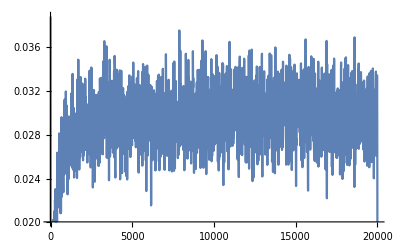

```mathematica
f=Interpolation[Take[data,{1,20000,10}]];
Plot[f[x],{x,1,20000}]
```

```mathematica
fp=Table[Prime[x],{x,20}]
Fit[fp,]
```

{0,0.25}

```mathematica
(*lsquared=50*50;
iterationsReported = 500;
m=Manipulate[
ListPlot[
Select[Take[data[[beta*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{i,0,iterationsReported,1,AnimationRate->50},{beta,0.1,0.9,0.1}]*)
```

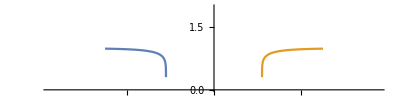

{0.0743315,0.925668,0.851337}

ItemAspectRatio::shdw: Symbol ItemAspectRatio appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/phase.png

Solve::naqs: Null is not a quantified system of equations and inequalities.

Solve[Null,beta]

```mathematica
mf[beta_] := (1-Csch[2*beta*1]^2)^(1/8);
ListLinePlot[{{#,mf[#]}&/@Range[-1,0,0.0001],{#,mf[#]}&/@Range[0,1,0.0001]},PlotRange->{{-1.5,1.5},{0,2}},AspectRatio->1/4,ImageSize->Full]
{(1-mf[0.5])/2,(1+mf[0.5])/2,mf[0.5]}
im = Plot[mf[beta],{beta,0,2},ImageSize->400,PlotRange->{{0,4},{0,2}},AspectRatio->0.9];
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/";
Export[path <> "phase.png",im]
Solve[,beta]
```

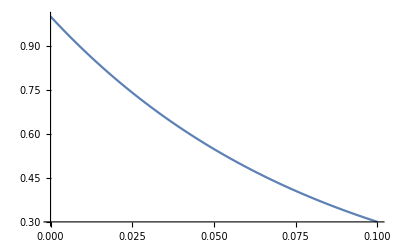

```mathematica
Plot[Exp[-beta*12],{beta,0,0.1}]
```

```mathematica
(*Table[path <> ToString[StringForm["cop``.txt", b]],{b,0.1,0.9,0.1}]*)
```

```mathematica
(*lsquared=50*50;
iterationsReported = 500;
m2[beta_]:=Manipulate[
ListPlot[
Select[Take[data[[beta*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{i,0,iterationsReported,1,AnimationRate->50}]
path ="/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/";
m2frames=Flatten@Table[m2[m1],{n1,0,iterationsReported,1},{m1,0.1,0.9,0.1}];
Export[path<> ToString[StringForm["COP_at_``.gif", 0.6]],frames]
(*Export[path<> ToString[StringForm["COP_at_``.gif", #]],m2[#]]&/@Range[0.1,0.9,0.1]*)*)
```

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/COP_at_0.6.gif

```mathematica
(*frames=Flatten@Table[Manipulate[ContourPlot[q1/Norm[{x,y}-p[[1]]]+q2/Norm[{x,y}-p[[2]]],{x,-2,2},{y,-2,2},Contours->20,PlotRangePadding->0,Frame->False,PlotPoints->40,ImageSize->230,ColorFunction->"DarkRainbow"],{{q1,n1},-3,3},{{q2,m1},-3,3},{{p,{{-1,0},{1,0}}},{-1,-1},{1,1},Locator},Deployed->True,FrameMargins->0],{n1,-3,3},{m1,-3,3}];
Export["~/Desktop/frames.gif",frames];*)
```

```mathematica
(*Export[path<> ToString[StringForm["COP_at_``.avi", 0.1]],m2[0.1]]*)
```

```mathematica
lsquared=50*50;
iterationsReported = 500/10;
myFrames=Flatten@
Table[Manipulate[
ListPlot[
Select[Take[data[[j]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1,PlotLabel -> Style[StringForm["β = ``, iteration = ``",betas[[j]],i],15]],
{{i,n1},0,iterationsReported,1},{{j,m1},Range[3],Slider},Deployed->True,FrameMargins->0],{m1,Range[3]},{n1,0,iterationsReported,1}];
path ="/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/";
Export[path<>"cop.gif",myFrames];

(*Export[path<> ToString[StringForm["COP_at_``.gif", #]],m2[#]]&/@Range[0.1,0.9,0.1]*)
```

```mathematica
(*lsquared=50*50;
iterationsReported = 10;
myFrames=Flatten@
Table[Manipulate[
ListPlot[
Select[Take[data[[0.5*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{{i,n1},0,iterationsReported,1},Deployed->True,FrameMargins->0],{n1,0,iterationsReported,1}];
path ="/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/";
Export[path<>"cop1.gif",myFrames];*)
```

```mathematica
(*lsquared=50*50;
iterationsReported = 500;
Manipulate[
ListPlot[
Select[Take[data[[1]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1, PlotLabel -> Style[StringForm["β = ``, iteration = ``",betas[[2]],i],15]],
{{i,500},0,iterationsReported,1}]*)
```

Take::take: Cannot take positions 1250001 through 1252500 in {{0,0,1},{0,1,1},{0,2,1},{0,3,1},{0,4,1},{0,5,1},{0,6,1},{0,7,1},{0,8,1},{0,9,1},{0,10,1},{0,11,1},{0,12,1},{0,13,1},{0,14,1},{0,15,1},{0,16,1},{0,17,1},{0,18,1},{0,19,1},{0,20,1},«9»,{0,30,-1},{0,31,-1},{0,32,-1},{0,33,-1},{0,34,-1},{0,35,-1},{0,36,-1},{0,37,-1},{0,38,-1},{0,39,-1},{0,40,-1},{0,41,-1},{0,42,-1},{0,43,-1},{0,44,-1},{0,45,-1},{0,46,-1},{0,47,-1},{0,48,-1},{0,49,-1},«27450»}.

Part::partw: Part 3 of {1250001,1252500} does not exist.

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

ListPlot::lpn: Take[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Take::take: Cannot take positions 1250001 through 1252500 in {{0,0,1},{0,1,1},{0,2,1},{0,3,1},{0,4,1},{0,5,1},{0,6,1},{0,7,1},{0,8,1},{0,9,1},{0,10,1},{0,11,1},{0,12,1},{0,13,1},{0,14,1},{0,15,1},{0,16,1},{0,17,1},{0,18,1},{0,19,1},{0,20,1},«9»,{0,30,-1},{0,31,-1},{0,32,-1},{0,33,-1},{0,34,-1},{0,35,-1},{0,36,-1},{0,37,-1},{0,38,-1},{0,39,-1},{0,40,-1},{0,41,-1},{0,42,-1},{0,43,-1},{0,44,-1},{0,45,-1},{0,46,-1},{0,47,-1},{0,48,-1},{0,49,-1},«27450»}.

Part::partw: Part 3 of {1250001,1252500} does not exist.

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

ListPlot::lpn: Take[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification data⟦1⟧ is longer than depth of object.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[data⟦1⟧,{1+500 lsquared,501 lsquared}].

Part::partd: Part specification data⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of data⟦1⟧ does not exist.

Part::partw: Part 3 of {1+500 lsquared,501 lsquared} does not exist.

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification betas⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::lpn: Take[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification data⟦1⟧ is longer than depth of object.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[data⟦1⟧,{1+500 lsquared,501 lsquared}].

Part::partd: Part specification data⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of data⟦1⟧ does not exist.

Part::partw: Part 3 of {1+500 lsquared,501 lsquared} does not exist.

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification betas⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::lpn: Take[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{0,0.25},{1+500 lsquared,501 lsquared}].

Part::partw: Part 3 of {0,0.25} does not exist.

Part::partw: Part 3 of {1+500 lsquared,501 lsquared} does not exist.

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification betas⟦2⟧ is longer than depth of object.

ListPlot::lpn: Take[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

0.20

```mathematica
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/COP/";
betas = {0.01,0.35,0.5}
path <> ToString[StringForm["cop``.txt", StringTrim@ToString@PaddedForm[#,{2,2}]]]&/@betas
```

{0.01,0.35,0.5}

{/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/COP/cop0.01.txt,/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/COP/cop0.35.txt,/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/COP/cop0.50.txt}

```mathematica
data[[1]]
```

$Aborted